Consider the classical C^∞bump function with support on (-1,1) rescaled so it has magnitude 1 at its center.

Piecewise[{{ⅇ^(x^2/(-1+x^2)), Abs[x]<1}, {0, True}}]

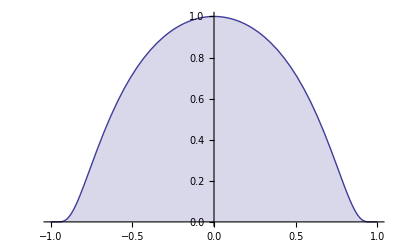

```mathematica
Bump[x_]:=Piecewise[{{Exp[x^2/(x^2-1)],Abs[x]  < 1}}]; Bump[x]
Plot[Bump[x],{x,-1,1},Filling->Axis]
```

Observe that the second derivative becomes large in magnitude near the edges of the support.  As the absolute value of the function and its derivatives is symmetric about the origin, only half of it is visualized.

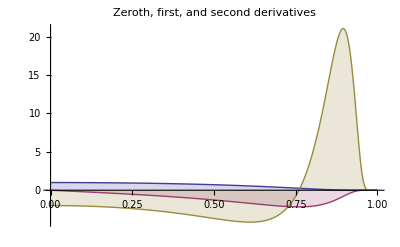

```mathematica
Plot[Evaluate[Table[Derivative[d][Bump][x],{d,0,2}]],
{x,0,1},Filling->Axis,PlotRange->Full,
PlotLabel->"Zeroth, first, and second derivatives"]
```

The magnitudes observed grow strikingly as the derivative order increases.

```mathematica
Table[{d,N[MaxValue[Abs[Derivative[d][Bump][x]],x]]},{d,0,7}]//MatrixForm
```

(0 | 1.
1 | 2.17036
2 | 21.0659
3 | 506.688
4 | 22604.9
5 | 1.62107×10^6
6 | 2.21471×10^8
7 | 3.95463×10^10)

This growth makes the bump function ill-suited for numerical initialization smoothing on coarse grids.  A coarse grid that can fully resolve the bump function will likely not be able to resolve its derivatives.  This lack of resolution may cause ringing to appear and can destabilize a simulation.  One fix would be to initialize with a Gaussian rather than a bump function.  However, Gaussian functions do not have compact support (and alleviating that issue in a C^∞-way brings one back again to bump functions).

One way to alleviate this problem is to use powers of the bump function to minimize the derivative magnitudes up to some finite derivative order.  Powers of the “magnitude-one” bump function still possess that same magnitude at x = 0 and remain C^∞.

Piecewise[{{ⅇ^((n x^2)/(-1+x^2)), Abs[x]<1}, {0, True}}]

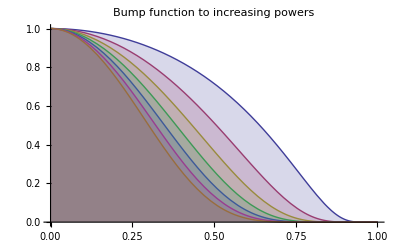

```mathematica
BumpPower[n_]:=Piecewise[{{Exp[(n #1^2)/(#1^2-1)],Abs[#1]  < 1}}] &;BumpPower[n][x]
Plot[Evaluate[Table[Derivative[0][BumpPower[power]][x],{power,1,7}]],
{x,0,1},Filling->Axis,PlotRange->Full,
PlotLabel->"Bump function to increasing powers"]
```

Derivative maximum magnitudes seem to decrease with the chosen power up to some limiting case.  After that case, the abruptness of the function’s magnitude increase at x = 0 dominates the behavior.

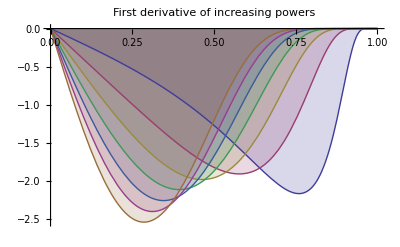

```mathematica
Plot[Evaluate[Table[Derivative[1][BumpPower[power]][x],{power,1,7}]],
{x,0,1},Filling->Axis,PlotRange->Full,
PlotLabel->"First derivative of increasing powers"]
```

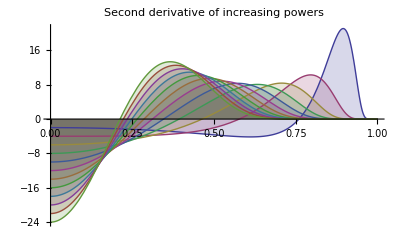

```mathematica
Plot[Evaluate[Table[Derivative[2][BumpPower[power]][x],{power,1,12}]],
{x,0,1},Filling->Axis,PlotRange->Full,
PlotLabel->"Second derivative of increasing powers"]
```

Spot checking a few powers suggests that low powers best control the second derivative.

```mathematica
MagnitudeBumpPowerDerivative[n_,d_]:=
N[MaxValue[Abs[Derivative[d][BumpPower[n]][x]],x]]
```

```mathematica
Table[MagnitudeBumpPowerDerivative[n,d],{d,0,5},{n,1,7}]//MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1.
2.17036 | 1.91156 | 1.98514 | 2.11782 | 2.26213 | 2.40592 | 2.54565
21.0659 | 10.2802 | 8.36423 | 8.06356 | 10. | 12. | 14.
506.688 | 127.416 | 73.0156 | 57.093 | 51.8527 | 62.4822 | 75.8722
22604.9 | 2881.99 | 1129.32 | 687.778 | 534.214 | 542.248 | 595.288
1.62107×10^6 | 103571. | 29124.4 | 14355.1 | 9722.52 | 8005.8 | 7479.46)

The table suggests that taking a power near four will optimally control the first and second derivative.  Attempting to minimize the derivative absolute magnitudes shows the following continous power-dependence:

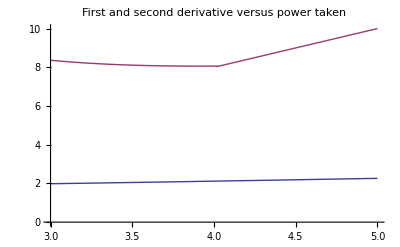

```mathematica
Plot[{
MagnitudeBumpPowerDerivative[n,1],
MagnitudeBumpPowerDerivative[n,2]
},{n,3,5},PlotRange->{All,{0,Full}},
PlotLabel->"First and second derivative versus power taken"]
```

Going to a non-integer power seems to buy very little benefit for the extra computational cost.  The integer power 4 seems to be a reasonable tradeoff between the first and second derivative’s maximum absolute magnitudes.

```mathematica
BumpPower[4][x]
```

Piecewise[{{ⅇ^((4 x^2)/(-1+x^2)), Abs[x]<1}, {0, True}}]

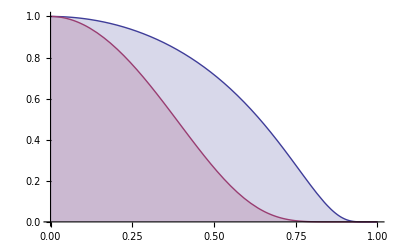

```mathematica
Plot[Evaluate[Table[Derivative[0][BumpPower[power]][x],{power,{1,4}}]],
{x,0,1},Filling->Axis,PlotRange->Full]
```

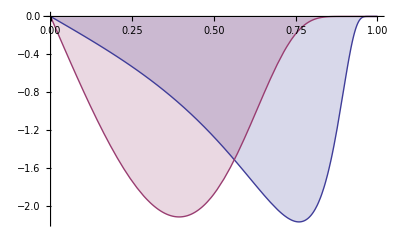

```mathematica
Plot[Evaluate[Table[Derivative[1][BumpPower[power]][x],{power,{1,4}}]],
{x,0,1},Filling->Axis,PlotRange->Full]
```

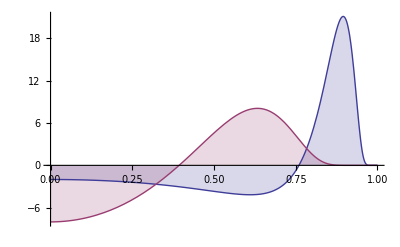

```mathematica
Plot[Evaluate[Table[Derivative[2][BumpPower[power]][x],{power,{1,4}}]],
{x,0,1},Filling->Axis,PlotRange->Full]
```

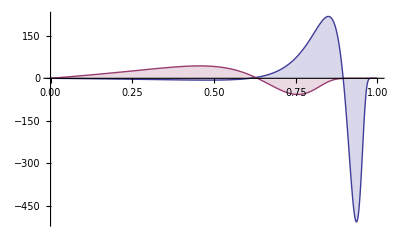

```mathematica
Plot[Evaluate[Table[Derivative[3][BumpPower[power]][x],{power,{1,4}}]],
{x,0,1},Filling->Axis,PlotRange->Full]
```